```mathematica
SetDirectory[NotebookDirectory[]];
```

# Pre

```mathematica
nff[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)-μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)-μ)/T]+1)];
nfa[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)+μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)+μ)/T]+1)];
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.))/T^2;
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.))/T^2;
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,1000,5000}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+(Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))/π^2)+λ;
h=6.5;
λ300=75.8;
ν300=-482.^2;
c300=1.7*10^-3*(10^3)^3;
λ400=56.3;
ν400=-482.^2;
c400=1.7*10^-3*(10^3)^3;
λ500=41.1;
ν500=-481.8^2;
c500=1.7*10^-3*(10^3)^3;
μ=0.;
M300=300;
M400=400;
M500=500;
```

# Mean-field effective potential

## effective potential

```mathematica
a=FindMinimum[{V[a1^2/2,h,1,0.,λ300,ν300,c300]+Vvacuum[a1^2/2,h,M300],0<a1<195},{a1,90},WorkingPrecision->8][[2]][[1]][[2]]//Quiet
(*a*√Zps[a^2/2,h,1.,0.,M1]*)
√Vd1rhovacuum[a^2/2,h,λ300,ν300,M300]
(*√((Vd1rhovacuum[a^2/2,h,λ,ν,M1]+2*a^2/2*Vd2rhovacuum[a^2/2,h,λ,ν,M1])/(Zps[a^2/2,h,1.,0.,M1]*0.+1.))
√mf2[h,a^2/2]
Plot[{(*V[a^2/2,h,1,0,λ,ν,c],Vvacuum[a^2/2,h,1000],*)V[a^2/2,h,1,0,λ,ν,c]+Vvacuum[a^2/2,h,M1]},{a,0,200},PlotRange->All]
Zps[a^2/2,h,1.,0.,300]*)
```

92.325526

135.695

```mathematica
(*fpi=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,μ,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];*)
```

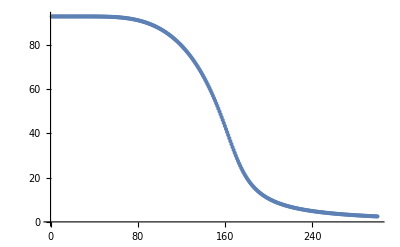

```mathematica
ListPlot[fpi,PlotRange->All]
```

# Mean-field wave function renormalization

## threshold functions

```mathematica
F2[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
```

## thermal equation

```mathematica
Zpsthr[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2[q,ρ,h,T,μ]+2/3 F3[q,ρ,h,T,μ]),{q,0.,500.,5000.}(*,{x,-1,1},{y,0,2π}*),AccuracyGoal->15,PrecisionGoal->15,MaxRecursion->20];
```

## Regularized vacuum

```mathematica
Zpsvac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[h,ρ])/M];
```

## Zps(0)

## Yukawa input data

```mathematica
hin[x_]:=a+b x+c1 x^2+d x^3+e x^4+f x^5+g x^6+h1 x^7+i x^8+j x^9/.{a->0.9957909545322429,b->0.001714257771479005,c1->-0.0001783382102583089,d->7.65973368936231*^-6,e->-1.5961805729197664*^-7,f->1.877596391835684*^-9,g->-1.3189343683401787*^-11,h1->5.429783784945215*^-14,i->-1.2017089289406018*^-16,j->1.1009372159449776*^-19};
```

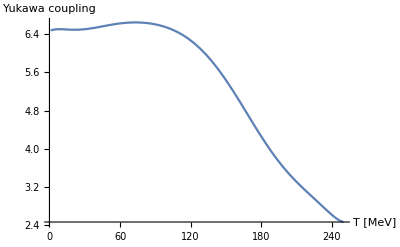

```mathematica
hplot=Plot[hin[x]*6.5,{x,1,250},AxesLabel->{"T [MeV]","Yukawa coupling"}]
```

```mathematica
Export["h.pdf",hplot]
```

h.pdf

```mathematica
hindata=Flatten[Table[hin[x]*6.5,{x,1,250}]];
```

## Z_π data

```mathematica
Zps[ρ_,h_,T_,μ_,M_]:=Zpsthr[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;
```

```mathematica
Zall=Flatten[Table[Zps[fpimub0[[i]]^2/2,h(*indata[[i]]*),N[i],0.,500.],{i,1,300}]];
(*Zvall=Flatten[Table[Zpsvac[fpi[[i]]^2/2,h,500.],{i,1,300}]];*)
(*Zvint=Flatten[Table[Zpsthr[fpi[[i]]^2/2,h,1.,μ],{i,1,300}]];*)
```

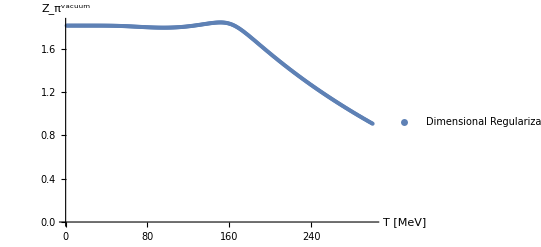

```mathematica
plotvac=ListPlot[{Zall},PlotRange->{{0,300},All},AxesLabel->{"T [MeV]","Z_π^vacuum"},PlotLegends->{"Dimensional Regularization  M=500 MeV","UV cut-off   Λ=700 MeV"}]
```

```mathematica
Export["./vac.pdf",plotvac]
```

./vac.pdf

# Mean-field two-point function

## threshold functions

```mathematica
F1[q_,ρ_,h_,T_,μ_]:=q/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1m[q_,p0_,ps_,x_,ρ_,h_,T_,μ_]:=q^3/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((*(-0.+nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))*)+((nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))(*+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))*));
```

## thermal equation

```mathematica
gamma2thr[p0_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^3 NIntegrate[q^2/q((*2F1[q,ρ,h,T,μ]*)-(p0^2+ps^2)/q^2 F1F1m[q,p0,ps,x,ρ,h,T,μ]),{q,0.,500.,1000.},{x,-1,1},{y,0,2π},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
(*gamma2thr0[p0_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^3NIntegrate[q^2/q(2F1[q,ρ,h,T,μ]),{q,0.,500.,5000.},{x,-1,1},{y,0,2π},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];*)
```

## Regularized vacuum

```mathematica
gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+(p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1}])-(Nc h^2 mf2[h,ρ])/(16 π^2);
```

## full two-point function

```mathematica
gamma2[p0_,ps_,ρ_,h_,T_,μ_,Mmass_,MZ_]:=gamma2thr[p0,ps,ρ,h,T,μ](*+gammavac[p0,ps,ρ,h,Mmass,MZ]*);
```

```mathematica
gammadata=Flatten[ParallelTable[gamma2[-ⅈ(i*10+ⅈ 0.5),j*50.,fpimu0[[100]]^2/2,h,100.,0.,700.,300.]+(-ⅈ(i*10))^2+(j*50.)^2+(λ fpimu0[[100]]^2/2+ν),{i,1,100},{j,1,20}]];
```

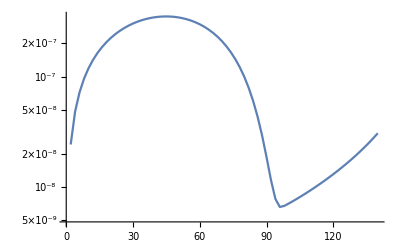

```mathematica
ListLinePlot[Transpose[{Flatten[Table[i*2,{i,1,70}]],-1/π Im[gammadata]/(Re[gammadata]^2+Im[gammadata]^2)}],PlotRange->All,ScalingFunctions->"Log"]
```

# Plot data

## fpi

```mathematica
mu={0,100,200,250,290,300};
```

```mathematica
fpiM300=ParallelTable[{FindMinimum[{V[a^2/2,h,i,mu[[j]],λ300,ν300,c300]+Vvacuum[a^2/2,h,M300],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{j,1,Length[mu]},{i,1,300}];
(*fpiM400=ParallelTable[{FindMinimum[{V[a^2/2,h,i,mu[[j]],λ400,ν400,c400]+Vvacuum[a^2/2,h,M400],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{j,1,Length[mu]},{i,1,300}];
fpiM500=ParallelTable[{FindMinimum[{V[a^2/2,h,i,mu[[j]],λ500,ν500,c500]+Vvacuum[a^2/2,h,M500],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{j,1,Length[mu]},{i,1,300}];*)
```

```mathematica
(*Export["./M300.dat",Flatten[fpiM300]];*)
(*Export["./M400.dat",Flatten[fpiM400]];
Export["./M500.dat",Flatten[fpiM500]];*)
```

```mathematica
fpi300=Flatten[Table[{Flatten[Import["./M300.dat"]][[300*(i-1)+1;;300*(i-1)+300]]},{i,1,Length[mu]}],1];
(*fpi400=Flatten[Table[{Flatten[Import["./M400.dat"]][[300*(i-1)+1;;300*(i-1)+300]]},{i,1,Length[mu]}],1];
fpi500=Flatten[Table[{Flatten[Import["./M500.dat"]][[300*(i-1)+1;;300*(i-1)+300]]},{i,1,Length[mu]}],1];*)
```

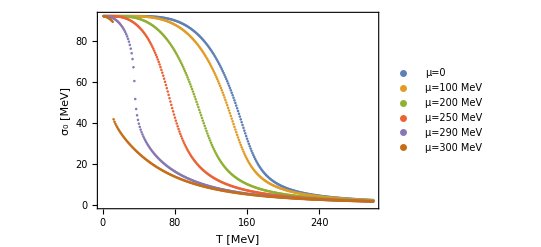

```mathematica
Plot1=ListPlot[fpi300,PlotStyle->{Automatic},PlotLegends->Placed[{"μ=0","μ=100 MeV","μ=200 MeV","μ=250 MeV","μ=290 MeV","μ=300 MeV"},{0.8,0.6}],Frame->True,FrameStyle->Black,FrameLabel->{Style["T [MeV]",Black],Style["σ_0 [MeV]",Black]}]
```

```mathematica
(*Export["sigma.pdf",Plot1]*)
```

## Z_π(p=0)

### M=300

```mathematica
(*Zmu0=Flatten[Table[Zps[(fpi300[[1]][[i]])^2/2,h,N[i],0.,300.],{i,1,300}]];
Zmu100=Flatten[Table[Zps[(fpi300[[2]][[i]])^2/2,h,N[i],100.,300.],{i,1,300}]];
Zmu200=Flatten[Table[Zps[(fpi300[[3]][[i]])^2/2,h,N[i],200.,300.],{i,1,300}]];
Zmu250=Flatten[Table[Zps[(fpi300[[4]][[i]])^2/2,h,N[i],250.,300.],{i,1,300}]];*)
Zmu290=Flatten[Table[Zps[(fpi300[[5]][[i]])^2/2,h,N[i],290.,300.],{i,1,300}]];
(*Zmu300=Flatten[Table[Zps[(fpi300[[6]][[i]])^2/2,h,N[i],300.,300.],{i,1,300}]];*)
```

```mathematica
ZplotM300=ListPlot[{Zmu0,Zmu100,Zmu200,Zmu250,Zmu290,Zmu300},PlotRange->{{-10,320},{-0.25,1.5}},PlotStyle->{Automatic},PlotLegends->Placed[{"μ=0","μ=100 MeV","μ=200 MeV","μ=250 MeV","μ=290 MeV","μ=300 MeV"},{0.86,0.69}],Frame->True,FrameStyle->Black,FrameLabel->{Style["T [MeV]",Black],Style["Z_π(0)",Black]}]
```

ListPlot::lpn: {{},{},{},{},{{1.,0.999685},{2.,0.998637},{3.,0.992931},{4.,0.98206},{5.,0.967802},{6.,0.951734},{7.,0.934829},{8.,0.917623},{9.,0.900397},{10.,0.883286},«290»},{}} 不是由数字或者数对组成的列表.

ListPlot[{Zmu0,Zmu100,Zmu200,Zmu250,{0.999685,0.998637,0.992931,0.98206,0.967802,0.951734,0.934829,0.917623,0.900397,0.883286,0.866344,0.849581,0.832981,0.816514,0.800137,0.783805,0.767465,0.751061,0.734529,0.717803,0.700807,0.683455,0.665647,0.64727,0.628182,0.608214,0.587147,0.564701,0.540489,0.513965,0.484302,0.450134,0.408927,0.355028,0.273763,0.187635,0.151036,0.132668,0.121454,0.113987,0.108829,0.105242,0.1028,0.101234,0.100365,0.100065,0.100241,0.100822,0.101751,0.102986,0.10449,0.106232,0.108188,0.110334,0.112651,0.115123,0.117734,0.12047,0.123318,0.126267,0.129306,0.132424,0.135613,0.138863,0.142166,0.145514,0.148899,0.152314,0.155753,0.159209,0.162675,0.166146,0.169617,0.173081,0.176533,0.17997,0.183386,0.186776,0.190137,0.193464,0.196754,0.200004,0.203209,0.206367,0.209475,0.21253,0.215529,0.218469,0.22135,0.224167,0.22692,0.229607,0.232225,0.234774,0.237252,0.239657,0.241989,0.244246,0.246428,0.248534,0.250562,0.252513,0.254386,0.25618,0.257896,0.259532,0.261089,0.262567,0.263966,0.265285,0.266525,0.267686,0.268768,0.269771,0.270697,0.271545,0.272315,0.273008,0.273625,0.274167,0.274633,0.275024,0.275342,0.275586,0.275758,0.275858,0.275886,0.275845,0.275733,0.275553,0.275305,0.27499,0.274609,0.274162,0.27365,0.273075,0.272436,0.271736,0.270974,0.270152,0.269271,0.268331,0.267334,0.266279,0.265169,0.264004,0.262785,0.261512,0.260187,0.25881,0.257382,0.255905,0.254379,0.252804,0.251182,0.249514,0.2478,0.246041,0.244238,0.242391,0.240503,0.238572,0.2366,0.234589,0.232537,0.230447,0.22832,0.226154,0.223953,0.221715,0.219443,0.217136,0.214795,0.212422,0.210016,0.207578,0.205109,0.20261,0.20008,0.197522,0.194935,0.19232,0.189678,0.187009,0.184313,0.181592,0.178846,0.176075,0.17328,0.170462,0.16762,0.164756,0.16187,0.158963,0.156035,0.153086,0.150117,0.147129,0.144121,0.141095,0.13805,0.134988,0.131908,0.128812,0.125699,0.122569,0.119424,0.116264,0.113089,0.109899,0.106695,0.103477,0.100245,0.0970007,0.0937433,0.0904735,0.0871916,0.0838979,0.0805927,0.0772764,0.0739492,0.0706115,0.0672636,0.0639057,0.0605381,0.0571612,0.0537752,0.0503804,0.046977,0.0435653,0.0401456,0.0367181,0.0332831,0.0298408,0.0263915,0.0229353,0.0194726,0.0160035,0.0125283,0.0090472,0.00556038,0.00206808,-0.00142951,-0.00493217,-0.00843971,-0.0119519,-0.0154686,-0.0189897,-0.0225148,-0.0260439,-0.0295767,-0.0331132,-0.036653,-0.0401961,-0.0437423,-0.0472914,-0.0508432,-0.0543977,-0.0579547,-0.0615139,-0.0650753,-0.0686388,-0.0722041,-0.0757711,-0.0793398,-0.0829099,-0.0864814,-0.0900541,-0.0936278,-0.0972026,-0.100778,-0.104354,-0.107931,-0.111509,-0.115087,-0.118665,-0.122243,-0.125821,-0.1294,-0.132978,-0.136556,-0.140133,-0.143711,-0.147287,-0.150863,-0.154439,-0.158013,-0.161587,-0.165159,-0.168731,-0.172302,-0.175871,-0.179439,-0.183006,-0.186571,-0.190135,-0.193697,-0.197258,-0.200817,-0.204374},Zmu300},PlotRange→{{-10,320},{-0.25,1.5}},PlotStyle→{Automatic},PlotLegends→Placed[{μ=0,μ=100 MeV,μ=200 MeV,μ=250 MeV,μ=290 MeV,μ=300 MeV},{0.86,0.69}],Frame→True,FrameStyle→GrayLevel[0],FrameLabel→{T [MeV],Z_π(0)}]

```mathematica
(*Export["Z.pdf",ZplotM300]*)
```

```mathematica
Zmu290M400=Flatten[Table[Zps[(fpi300[[5]][[i]])^2/2,h,N[i],290.,400.],{i,1,300}]];
Zmu290M500=Flatten[Table[Zps[(fpi300[[5]][[i]])^2/2,h,N[i],290.,500.],{i,1,300}]];
```

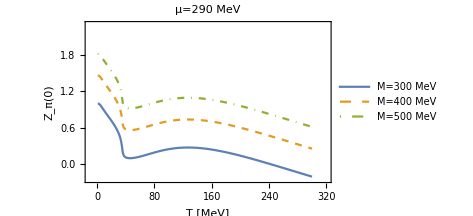

```mathematica
p1=ListLinePlot[{Zmu290,Zmu290M400,Zmu290M500},PlotRange->{{-10,320},{-0.25,2.3}},PlotStyle->{Automatic,Dashed,DotDashed},PlotLegends->Placed[{"M=300 MeV","M=400 MeV","M=500 MeV"},{0.8,0.75}],PlotLabel->Style["μ=290 MeV",Black],Frame->True,FrameStyle->Black,FrameLabel->{Style["T [MeV]",Black],Style["Z_π(0)",Black]},ImageSize->350];
p2=ListLinePlot[{Zmu290-Zmu290[[1]]+1,Zmu290M400-Zmu290M400[[1]]+1,Zmu290M500-Zmu290M500[[1]]+1},PlotRange->{{-10,320},{-0.25,1.2}},PlotStyle->{Automatic,Dashed,DotDashed},Frame->True,FrameStyle->Black(*,FrameLabel->{Style["T [MeV]",Black],Style["Z_π(0)",Black]}*),ImageSize->130,FrameTicksStyle->Directive[Black,FontSize->6]];
Plot2=Graphics[{Inset[p1],Inset[p2,Scaled[{0.45,0.73}]]},AspectRatio->0.7]
```

```mathematica
Export["Zmu290M300.dat",Zmu290];
Export["Zmu290M400.dat",Zmu290M400];
Export["Zmu290M500.dat",Zmu290M500];
```